# Efficiency Comparison

## Defining Methods and Preamble

## Preamble

```mathematica
(*Set directory paths.*)
SetDirectory[NotebookDirectory[]];
```

## Plotting Method

```mathematica
makeBoxCMS[data_,labels_,yLabel_,cmsPos_,tevPos_,precY_:1,xLabelY_:0.06]:=Module[{majorLen,minorLen,makeTicks01,yVals,yTicks,yTicksRight,plot,cmsText,tevText,plotLeft=0.01,plotBottom=0.12,plotWidth=0.98,plotHeight=0.84,xCenters},majorLen=Scaled[0.015];
minorLen=Scaled[0.015/2];
makeTicks01[{vmin_?NumericQ,vmax_?NumericQ},prec_]:=Module[{maj,min},maj=N@FindDivisions[{vmin,vmax},6];
min=N@Flatten@Table[Most@Rest@Subdivide[maj[[k]],maj[[k+1]],6],{k,1,Length[maj]-1}];
Join[({#,NumberForm[#,{6,prec}],{majorLen,0}}&/@maj),({#,"",{minorLen,0}}&/@min)]];
yVals=Flatten[data];
yTicks=makeTicks01[{0,1.05 Max[yVals]},precY];
yTicksRight=yTicks/. {v_,_,len_}:>{v,"",len};

plot=BoxWhiskerChart[
data,
{"Outliers",
{"MedianMarker",1.0,Directive[Yellow,AbsoluteThickness[3]]},
{"Whiskers",Directive[Black,AbsoluteThickness[3]]},
{"Fences",0.5,Directive[Black,AbsoluteThickness[2]]},
{"Outliers",Directive[Black,AbsolutePointSize[5]]}
},

ChartStyle->Table[Directive[RGBColor["#3f90da"],Opacity[0.85]],{Length[data]}],
Frame->True,Axes->False,
FrameTicks->{{yTicks,yTicksRight},{Automatic,Automatic}},
FrameStyle->Directive[Black,AbsoluteThickness[2]],
FrameTicksStyle->Directive[Black,FontSize->22,FontFamily->"TeX Gyre Heros"],
LabelStyle->Directive[Black,FontSize->24,FontFamily->"TeX Gyre Heros"],
FrameLabel->{None,Style[yLabel,Black,FontSize->30,FontFamily->"TeX Gyre Heros"]},
GridLines->{None,Automatic},GridLinesStyle->Directive[GrayLevel[0.85]],
ImageSize->1300,AspectRatio->0.5,ImagePadding->{{100,40},{40,40}},PlotRange->{0,1.05 Max[yVals]},
PlotRangePadding->{{Scaled[-0.1],Scaled[0.02]},{Scaled[0.05],Scaled[0.01]}}
];

cmsText=Row[{Style["CMS",Bold,FontFamily->"TeX Gyre Heros",24],Style[" Simulation Preliminary",Italic,FontFamily->"TeX Gyre Heros",24]}];
tevText=Style["14 TeV",FontFamily->"TeX Gyre Heros",24];
xCenters={0.19, 0.36,0.535, 0.71};

Graphics[Join[{Inset[plot,Scaled[{plotLeft,plotBottom}],{Left,Bottom},Scaled[{plotWidth,plotHeight}]]},Table[Inset[Style[labels[[i]],FontFamily->"TeX Gyre Heros",22],Scaled[{xCenters[[i]],xLabelY}],{Center,Top}],{i,Length[labels]}],{Inset[cmsText,Scaled[cmsPos],{Left,Bottom}],Inset[tevText,Scaled[tevPos],{Right,Bottom}]}],PlotRange->{{0,1},{0,1}},AspectRatio->0.5,ImageSize->1300]]
```

## Data Plots

## Efficiency Plot: AE @ 250 Hz

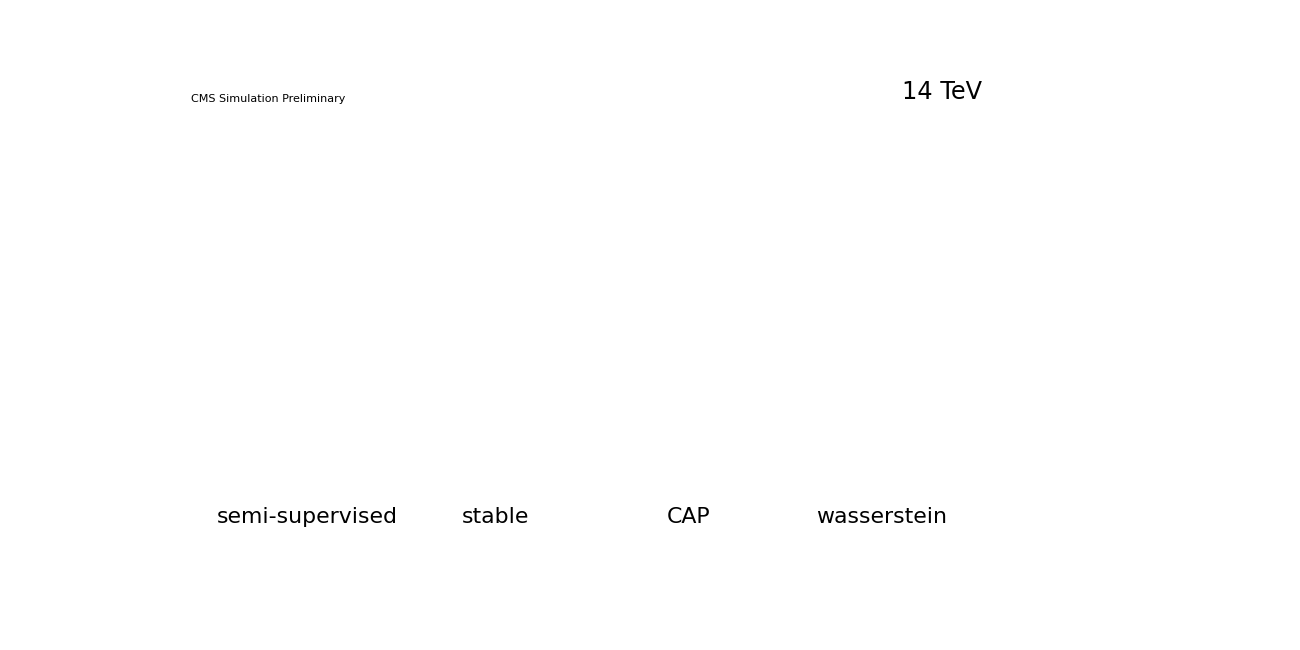

effs/ae_250Hz.svg

```mathematica
(*Data*)
semisupervised={0.45,0.36,0.00,0.02,0.75,0.63,0.79,6.20,6.56,16.19,0.60,0.03,11.55,6.75,5.95,1.96,0.25,0.54,2.14,10.89};
stable={1.39,0.35,0.00,0.07,0.75,0.62,0.66,9.86,10.23,14.59,0.54,0.03,12.75,9.71,8.46,2.85,0.28,0.19,0.28,11.92};
CAP={2.07,0.38,0.00,0.11,0.76,0.64,0.72,11.60,12.13,16.33,0.56,0.03,13.70,10.82,9.71,3.09,0.27,0.21,0.34,12.34};
wasserstein={0.17,0.23,0.00,0.03,0.87,0.62,0.72,6.85,6.96,15.79,0.56,0.03,13.12,6.98,6.46,2.69,0.27,0.22,0.42,10.77};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.8,0.9},1,0.17]
Export["effs/" <> "ae_250Hz" <>".svg",plot,"SVG"]
```